# MGDrivE: Yorkeys Knob Analysis

## 0) Functions

```mathematica
<<colorBlender`
rgbColors={
ColorData[{"LakeColors",{1,0}}][1],
ColorData[{"LakeColors",{1,0}}][0]
};
GenerateBlendSetting[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
GenerateBlendSettingCMYK[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
hexifyColor[color_RGBColor]:=StringJoin["#",IntegerString[Round[Level[color,1]*255],16,2]]
hexToRGB=RGBColor@@(IntegerDigits[ToExpression@StringReplace[#,"#"->"16^^"],256,3]/255.)&;
FixDataEntry[dataFileContent_]:=Append[#,#//Total]&/@(dataFileContent[[2;;All,2;;All]][[All,1;;(Length[dataFileContent[[1]]]-1)]])
PlotDynamics[data_,ranges_,colorPalette_,plotLabels_]:=Module[{plotRight,plotLeft},
(**)
plotLeft=ListLinePlot[
data//Transpose,
AspectRatio->1,
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->Large,
PlotRange->{{0,ranges[[1]]},{0,ranges[[2]]}},
FrameStyle->{
{Thick,Thick},
{Thick,Thick}
},
FrameTicks->Automatic,
FrameLabel->(Style[#,30]&/@plotLabels)
]
]
Themes`AddThemeRules["MGDrivE_PopDyn",
DefaultPlotStyle->Thread@Directive[colorPalette,Thickness[.01]],
LabelStyle->15,
Frame->True,
FrameStyle->Directive[Thick,Gray],
FrameTicksStyle->Gray,
GridLines->Automatic,
PlotRange->{0,All},
ImageSize->Large,
FrameLabel->(Style[#,30]&/@{"Time","Population"})
];
Options[SplitPlotDynamics]={AspectRatios->{.75,.45},ImageSize->500};
SplitPlotDynamics[data_,ranges_,colorPalette_,OptionsPattern[]]:=Module[{plotRight,plotLeft,rangeA=ranges[[1]],rangeB=ranges[[2]]},
(**)
plotLeft=ListLinePlot[
data//Transpose,
AspectRatio->1/OptionValue[AspectRatios][[1]],
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->{Automatic,OptionValue[ImageSize]},
PlotRange->{rangeA,{0,Round[(Flatten[data]//Max)*.1]+(Flatten[data]//Max)}},
FrameStyle->{
{Thick,Dashed},
{Thick,Thick}
},
FrameTicks->{{Automatic,None},{Range[0,rangeA[[2]]-1,100],None}},
FrameLabel->(Style[#,30]&/@{"Time","Population"})
];
plotRight=ListLinePlot[
data//Transpose,
AspectRatio->1/OptionValue[AspectRatios][[2]],
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->{Automatic,OptionValue[ImageSize]},
PlotRange->{rangeB,{0,Round[(Flatten[data]//Max)*.1]+(Flatten[data]//Max)}},
FrameStyle->{
{Dashed,Thick},
{Thick,Thick}
},
FrameTicks->{{None,All},{Range[0,rangeB[[2]]-1,500],None}},
FrameLabel->(Style[#,30,White]&/@{"Time","Population"})
];
Grid[{{plotLeft,plotRight}},Spacings->{0,0}]
]

ImportAndReshapeData[folderName_]:=Module[{fileNames,raw,data,dataTotal,maleFileNames,femaleFileNames,rawMale,rawFemale,dataMale,dataFemale,dataTotalMale,dataTotalFemale,genotypes},
fileNames={maleFileNames,femaleFileNames}=FileNames[folderName<>"/"<>#]&/@{"ADM*.csv","AF1_Aggregate*.csv"};
raw={rawMale,rawFemale}=Table[ParallelMap[Import[#]&,i],{i,fileNames}];
data={dataMale,dataFemale}=Table[#[[2;;All,3;;All]]&/@i,{i,raw}];
dataTotal={dataTotalMale,dataTotalFemale}=Table[Flatten/@Transpose[{Total/@#,#}]&/@i,{i,data}];
genotypes=Prepend[rawMale[[1,1,3;;All]],"Total"];
{genotypes,dataTotal}
]
CalculateQuartiles[genotypes_,data_]:=Module[{sexes,quartilesData,lowQuartile,medianQuartile,topQuartile},
sexes=2;
Table[
quartilesData=Table[Transpose[Quartiles/@Transpose[data[[j]][[All,All,i]]]],{i,1,genotypes//Length}];
{lowQuartile,medianQuartile,topQuartile}={quartilesData[[All,1]]//Transpose,quartilesData[[All,2]]//Transpose,quartilesData[[All,3]]//Transpose}
,{j,1,sexes}]
]
CreateColorSwatch[genotypes_,colorSchemeNumber_,{markerSize_,labelStyle_}]:=Module[{colorPalette,colorPairs,colorSwatch},
colorPalette=Prepend[ColorData[colorSchemeNumber,"ColorList"][[1;;(Length[genotypes]-1)]],Lighter[Black,.75]];
colorPairs=Transpose[{genotypes,colorPalette}];
colorSwatch=SwatchLegend[colorPairs[[All,2]],colorPairs[[All,1]],LegendMarkerSize->markerSize,LabelStyle->labelStyle,LegendLayout->{"Column",1}];
{colorPalette,colorSwatch}
]
ReshapeSexData[sexData_,quantile_]:=Module[{nodeDataAtTime,reshapedData},
reshapedData=Table[
Table[
nodeDataAtTime=Transpose[sexData][[node,All,time]];
Quantile[#,quantile]&/@Transpose[nodeDataAtTime]
,{time,1,sexData[[1,1]]//Length}]
,{node,1,sexData[[1]]//Length}];
reshapedData
]
ReshapeStochasticMultiNode[dataTotal_,quantile_]:=ParallelTable[ReshapeSexData[dataTotal[[All,i]],quantile],{i,1,2}]
AddLabelsToReshapedDataNode[reshapedDataNode_,genotypes_,patchNumber_]:=Module[{breakdownWithPop,breakdownWithTime,labels},
breakdownWithPop=Prepend[#,patchNumber]&/@reshapedDataNode[[All,2;;All]];
breakdownWithTime=Prepend[#[[2]],#[[1]]]&/@Transpose[{Range[breakdownWithPop//Length],breakdownWithPop}];
labels=Prepend[ReplacePart[genotypes,1->"Patch"],"Time"];
Prepend[breakdownWithTime,labels]
]
```

```mathematica
SmoothHistogramPlot[sampledCoordinatesLayer_,{imageSize_,imagePadding_},plotRange_]:=SmoothHistogram[sampledCoordinatesLayer,
PlotStyle->Directive[{Thickness[.01],Opacity[.5]}],
ImageSize->imageSize,
PlotRange->{plotRange[[1]],plotRange[[2]]},
AspectRatio->.075,
Axes->False,
FrameStyle->Directive[Thick,Gray],
FrameTicks->{None,None},
Filling->Bottom,
Frame->True,
FrameLabel->None,
ImagePadding->imagePadding,
ImageSize->imageSize,
PlotTheme->"RandomPointsPlot"
]
ListPlotScatter[clusteredCoordinates_,{imageSize_,imagePadding_},plotRange_]:=
ListPlot[clusteredCoordinates,
FrameTicks->Automatic,
FrameStyle->Directive[Thick,Gray],
Axes->False,
GridLines->Automatic,
BaseStyle->15,
Frame->True,
AspectRatio->1,
LabelStyle->Directive[10],
FrameLabel->{{None,Rotate["y [meters]",180Degree]},{None,"x [meters]"}},
PlotRange->{plotRange[[1]],plotRange[[1]]},
PlotTheme->"RandomPointsPlot",
PlotStyle->Directive[{PointSize[.025],Red,Opacity[.35]}],
ImageSize->imageSize,
ImagePadding->imagePadding
]
CalculateEuclideanDistances[coordinates_]:=Table[N[EuclideanDistance[coordinates[[i]],#]]&/@coordinates,{i,1,coordinates//Length }]
<<PajaroLocoPublic`
SetDirectory[NotebookDirectory[]];
ImportAndReshapeMosquitoDatasets[dataPath_,{maleFilenamePattern_,femaleFilenamePattern_}]:=Module[{names,dataSets,maleFilenames,femaleFilenames,maleDatasets,femaleDatasets,genotypes,ticksMax,maleMax,femaleMax},
maleFilenames=FileNames[maleFilenamePattern<>"_*.csv",dataPath]//Sort;
femaleFilenames=FileNames[femaleFilenamePattern<>"_Aggregate*.csv",dataPath]//Sort;
maleDatasets=AddTotalPopulationToDataset[Map[Import[#][[2;;All,2;;All]]&,maleFilenames]];
femaleDatasets=AddTotalPopulationToDataset[Map[Import[#][[2;;All,2;;All]]&,maleFilenames]];
genotypes=Import[maleFilenames[[1]]][[1,3;;All]];
ticksMax=Length[maleDatasets[[1]]];
{maleMax,femaleMax}={Flatten[maleDatasets]//Max,Flatten[femaleDatasets]//Max};
(*Output*)
{
{maleDatasets,femaleDatasets},
{genotypes,ticksMax,{maleMax,femaleMax}}
}
]
GenerateColorPalette[genotypes_,colorScheme_]:=Module[{steps,colors},
steps=(genotypes//Length)-1;
colors={ColorData[colorScheme,#]&/@Range[0,1,1/steps],Black}//Flatten;
{Append[genotypes,"Total"],colors}
]
ImportGeoCoordinatesAndKernel[coordinatesFilePath_,kernelFilePath_]:=Module[{cities,transitionsMatrix},
cities={#[[1]],{#[[2]],#[[3]]},#[[4]]}&/@Import[coordinatesFilePath];
transitionsMatrix=Import[kernelFilePath][[2;;All]];
{cities,transitionsMatrix}
]
AddTotalPopulationToDataset[dataset_]:=Table[Append[#,Total[#]]&/@dataset[[i]],{i,1,Length[dataset]}]
AggregatePopulationByGenotypeIndices[populationDatasets_,genotypesIndicesToAggregate_]:=Module[{popsDatasets,geneLabels},
popsDatasets=Table[Transpose[Total/@populationDatasets[[i,All,#[[2]]]]&/@genotypesIndicesToAggregate],{i,1,Length[populationDatasets]}];
geneLabels=genotypesIndicesToAggregate[[All,1]];
{geneLabels,AddTotalPopulationToDataset[popsDatasets]}
]
AggregatePopulationAcrossNodes[aggregatedPopulations_]:=Table[Total/@(aggregatedPopulations[[All,i]]//Transpose),{i,1,Length[aggregatedPopulations[[1]]]}]
SubsetPopulations[{aggregatedPopulations_,aggregatedPopulationsAcrossNodes_},dataRange_]:={aggregatedPopulations[[All,dataRange[[1]];;dataRange[[2]]]]//Transpose,aggregatedPopulationsAcrossNodes[[dataRange[[1]];;dataRange[[2]]]]}
GeneratePopCountsFrames[{labels_,colors_},subsetPopulationsAccrossNodes_]:=Module[{styledLabels,styledNumbers,gridFrames},
styledLabels=Style[#,30]&/@labels;
styledNumbers=Table[Style[Round[#],30,Gray]&/@Threshold[i,{"Hard",10^-1}],{i,subsetPopulationsAccrossNodes}];
gridFrames=Table[
Grid[{styledLabels,styledNumbers[[i]]}//Transpose,
Frame->True,
FrameStyle->Thick,
ItemSize->40,
Background->{None,Opacity[.25,#]&/@colors},
Alignment->Center
]
,{i,1,subsetPopulationsAccrossNodes//Length}]
]


ExportFrames[plots_,dataRange_,{outputBasePath_,outputFolder_,filesBaseName_}]:=Module[{namesStrings,pathsStrings},
namesStrings=(filesBaseName<>StringPadLeft[ToString[#],6,"0"]<>".png")&/@Range[dataRange[[1]],dataRange[[2]]];
pathsStrings=(outputBasePath<>outputFolder<>#)&/@namesStrings;
Export[#[[1]],#[[2]]]&/@Transpose[{pathsStrings,plots}]
]
BarChartPopDynamicsMaskFrames[fullRaster_,{tick_,ticksMax_}]:=Module[{rasterDimensions,stepSize,composedImage,day=tick},
rasterDimensions=ImageDimensions[fullRaster];
stepSize=rasterDimensions[[1]]/ticksMax//N;
composedImage=ImageCompose[
fullRaster,
Graphics[{
Yellow,Opacity[0],Rectangle[{0,0},{rasterDimensions[[1]],rasterDimensions[[2]]}],
Black,Opacity[1],Rectangle[{day*stepSize,0},{day*stepSize+2*stepSize,rasterDimensions[[2]]}],
White,Opacity[.75],Rectangle[{day*stepSize+2*stepSize*stepSize,0},{rasterDimensions[[1]],rasterDimensions[[2]]}]
},
ImageSize->rasterDimensions[[1]],
AspectRatio->1/5,
ImagePadding->None,
ImageMargins->0,
PlotRangePadding->None
]
]
]
ParseFilenames[tick_,{outputFolder_,{outputPopCounts_,outputBarCharts_,outputFlow_,outputNetworks_},{baseCounts_,baseDays_,baseBarCharts_,basePopDyn_,baseNetworks_}}]:=Module[{paddedNumber,rastersFolders,rastersNames},
paddedNumber=StringPadLeft[ToString[tick],6,"0"];
rastersFolders=(outputFolder<>#)&/@{outputPopCounts,outputBarCharts,outputFlow,outputNetworks};
rastersNames=(#<>paddedNumber<>".png")&/@{baseCounts,baseDays,baseBarCharts,basePopDyn,baseNetworks};
{
rastersFolders[[1]]<>rastersNames[[1]],
rastersFolders[[1]]<>rastersNames[[2]],
rastersFolders[[2]]<>rastersNames[[3]],
rastersFolders[[3]]<>rastersNames[[4]],
rastersFolders[[4]]<>rastersNames[[5]]
}
]
GenerateAnimationFrameFromFiles[fileNameTuple_]:=Module[{popCount,dayCount,barChart,flow,network,row},
{popCount,dayCount,barChart,flow,network}=Import[#]&/@fileNameTuple;
row=Grid[{{ImageRotate[barChart,90Degree]//Show[#]&,dayCount//Show[#]&,network//Show[#]&,popCount//Show[#]&,ImageRotate[flow,90Degree]//Show[#]&}}];
Rasterize[row]
]
GeneratePieChartsAtTick[subsetPopulation_,labels_,maxPop_]:=Module[{chartAndPop},
chartAndPop={
PieChart[#,ChartStyle->colors,BaseStyle->Directive[EdgeForm[Thickness[.07]]],ColorFunction->(EdgeForm[Black]&),PerformanceGoal->"Speed"],
Total[#]
}&/@(subsetPopulation[[All,1;;(Length[labels]-1)]]);
{#[[1]],Sqrt[#[[2]]/maxPop]}&/@chartAndPop
]
BarChartPopDynamicsFrames[tick_,aggregatedPopulationsAcrossNodes_,{colors_,maxPop_,ticksMax_,frameDimensions_,labels_},ticks_]:=Module[{dataUntilTick},
dataUntilTick=aggregatedPopulationsAcrossNodes[[1;;tick]][[All,1;;(Length[labels]-1)]];
BarChart[dataUntilTick,
ChartLayout->"Stacked",
ChartStyle->{EdgeForm[None],(Directive[Opacity[1],#]&/@colors )},
Frame->True,
FrameStyle->Directive[Thick,Black],
FrameTicks->ticks,
FrameTicksStyle->17.5,
PlotRange->{{0,ticksMax},{0,maxPop}},
Axes->False,
PerformanceGoal->"Speed",
AxesLabel->(Style[#,40]&/@{"Time","Genotype Breakdown"}),
BarSpacing->{0,0},
AspectRatio->1/3,
PlotRangePadding->{0,0},
BarOrigin->Bottom,
ImageSize->1000(*frameDimensions[[1]]*) ,
Epilog->Flatten[{Lighter[Gray,.5],Thickness[.0005],Opacity[.5],(Line[{{#,0},{#,maxPop}}]&/@Range[0,ticksMax,250]),(Line[{{0,#},{ticksMax,#}}]&/@Range[0,maxPop,1000])}]
]
]
PlotDynamics[data_,ranges_,colorPalette_,plotLabels_,tag_]:=Module[{plotRight,plotLeft},
plotLeft=ListLinePlot[
data//Transpose,
AspectRatio->1,
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->Large,
PlotRange->{{0,ranges[[1]]},{0,ranges[[2]]}},
FrameStyle->{
{Thick,Thick},
{Thick,Thick}
},
FrameTicks->Automatic,
FrameTicksStyle->Directive[Gray,18],
FrameLabel->(Style[#,40]&/@plotLabels),
Epilog->Style[Text[tag,{900,550}],Directive[Gray,35]]
]
]
CreateColorBlend[genotypes_,colorSchemeName_,{markerSize_,labelStyle_}]:=Module[{colorPalette,colorPairs,colorSwatch},
colorPalette=Prepend[ColorData[colorSchemeName][#]&/@Range[0,1,1/(Length[genotypes]-1)],Lighter[Black,.75]];
colorPairs=Transpose[{Prepend[genotypes[[All,1]],"Total"],colorPalette}];
colorSwatch=SwatchLegend[colorPairs[[All,2]],colorPairs[[All,1]],LegendMarkerSize->markerSize,LabelStyle->labelStyle,LegendLayout->{"Column",1}];
{colorPalette,colorSwatch}
]
```

## 1) Factorial Grid

Setup work folder (to root where files are located)

```mathematica
CASE=6;
If[CASE==0,SetDirectory["/Volumes/marshallShare/ThresholdResub/tnFactorialSweep/MigrationNo/"]]
If[CASE==1,SetDirectory["/Volumes/marshallShare/ThresholdResub/tnFactorialSweep/MigrationYes/"]]
If[CASE==2,SetDirectory["/Volumes/marshallShare/ThresholdResub/tnFactorialSA/"]]
If[CASE==3,SetDirectory["/Volumes/marshallShare/ThresholdResub/tnFactorialSweep/"]]
If[CASE==4,SetDirectory["/Volumes/marshallShare/ThresholdResub/tnBatchSA/"]]
If[CASE==5,SetDirectory["/Volumes/marshallShare/ThresholdResub/tnFactorialSA/sensitivity/"]]
If[CASE==6,SetDirectory["/Volumes/marshallShare/ThresholdResub/factorialSweep/"]](*YK_BioParams/"]]*)
If[CASE==7,SetDirectory["/Volumes/marshallShare/ThresholdResub/factorialSweep/Wolbachia/ANALYZED/"]]
If[CASE==8,SetDirectory["/Volumes/marshallShare/ThresholdResub/factorialSweep/SweepSummaries/ResolutionDifferences/"]]
If[CASE==9,SetDirectory["/Volumes/marshallShare/ThresholdResub/factorialHP/"]]
If[CASE==10,SetDirectory["/Volumes/marshallShare/ThresholdResub/factorialHP/ResolutionDifferences/"]]
If[CASE==11,SetDirectory["/Volumes/marshallShare/ThresholdResub/batchSweep/"]]
If[CASE==12,SetDirectory["/Volumes/marshallShare/ThresholdResub/tnBatchSweep/"]]
If[CASE==13,SetDirectory["/Volumes/marshallShare/ThresholdResub/fReRun/"]]
If[CASE==14,SetDirectory["/Volumes/marshallShare/ThresholdResub/tnBatchSA/sensitivity/"]]
If[CASE==15,SetDirectory["/Volumes/marshallShare/ThresholdResub/factorialSA/sensitivity/"]]
If[CASE==16,SetDirectory["/Volumes/marshallShare/ThresholdResub/factorialSA/"]]
If[CASE==17,SetDirectory["/Volumes/marshallShare/ThresholdResub/batchSA/sensitivity/"]]
If[CASE==18,SetDirectory["/Volumes/marshallShare/ThresholdResub/batchSA/"]]
If[CASE==19,SetDirectory["/Volumes/marshallShare/ThresholdResub/tnBatchSweep/ResolutionDifferences/"]]
If[CASE==20,SetDirectory["/Volumes/marshallShare/ThresholdResub/batchHP/"]]
If[CASE==21,SetDirectory["/Volumes/marshallShare/ThresholdResub/batchHP/sensitivity/"]]
(**)
timeRange={1,1093};
pops={15*923,15*1301};
popsRatio=pops[[1]]/(pops[[2]]+pops[[1]])//N;
experimentsList =Cases[Sort[(StringSplit[#,"."][[1]])&/@ FileNames["*.csv"]],a_/;StringTake[a,1]≠"_"]
```

/Volumes/marshallShare/ThresholdResub/factorialSweep

{Translocations,TranslocationsRemediation,UDMel,UDMelRemediation,Wolbachia,WolbachiaRemediation}

## Current

Response Surface: SA

```mathematica
cf1=(Blend[{Directive[{hexToRGB["#ffffff"],Opacity[1]}],Directive[{RGBColor[1, 0, 0.5],Opacity[.85]}]},#1]&);
Table[
day=timeRange[[2]];
flattenedData={#[[1]],#[[2]],Round[#[[3]]],#[[4]]}&/@ToExpression[Import[experiment<>".csv"]];
x=If[( Length[StringCases[experiment,_~~"R"~~_]]<1),0,1];
filtered=Cases[flattenedData,{a_,b_,day,c_}->{a,b,c}];
{firstCol,firstRow}=ConstantArray[x,2];
contour=ListContourPlot[
Flatten[{
{#[[1]],#[[2]],Clip[#[[3]],{0,1}]}&/@filtered,
Transpose[{
ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],
flattenedData[[All,2]]//DeleteDuplicates,
ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length]
}],
Transpose[{
flattenedData[[All,1]]//DeleteDuplicates,
ConstantArray[firstRow,flattenedData[[All,1]]//DeleteDuplicates//Length],
ConstantArray[firstRow,flattenedData[[All,1]]//DeleteDuplicates//Length]
}]
},1]
,ColorFunction->cf1
,ColorFunctionScaling->False
,GridLines->{Range[-.5,20.5,1],Range[-1.025,1.05,.05]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
,FrameTicks->{{{#,ToString[#*100//Round]}&/@Range[0,1,.25],None},{Range[0,25,5],None}}
,FrameTicksStyle->Directive[65]
,PlotRange->{{-.5,20.5},{-.025,1.025},{0,1}}
,PlotRangePadding->0
];
Export["./images/"<>experiment<>".png",contour,ImageResolution->500];
Print[experiment];
,{experiment,experimentsList}]
```

Translocations_0001

Translocations_0002

Translocations_0010

Translocations_0020

Translocations_0100

Translocations_0200

Translocations_1000

Translocations_2000

TranslocationsRemediation_0001

TranslocationsRemediation_0002

TranslocationsRemediation_0010

TranslocationsRemediation_0020

TranslocationsRemediation_0100

TranslocationsRemediation_0200

TranslocationsRemediation_1000

TranslocationsRemediation_2000

UDMel_0001

UDMel_0002

UDMel_0010

UDMel_0020

UDMel_0100

UDMel_0200

UDMel_1000

UDMel_2000

UDMelRemediation_0001

UDMelRemediation_0002

UDMelRemediation_0010

UDMelRemediation_0020

UDMelRemediation_0100

UDMelRemediation_0200

UDMelRemediation_1000

UDMelRemediation_2000

Wolbachia_0001

Wolbachia_0002

Wolbachia_0010

Wolbachia_0020

Wolbachia_0100

Wolbachia_0200

Wolbachia_1000

Wolbachia_2000

WolbachiaRemediation_0001

WolbachiaRemediation_0002

WolbachiaRemediation_0010

WolbachiaRemediation_0020

WolbachiaRemediation_0100

WolbachiaRemediation_0200

WolbachiaRemediation_1000

WolbachiaRemediation_2000

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

Response Surface: Fixation/Remediation for Two Nodes

```mathematica
cf1=(Blend[{Directive[{hexToRGB["#ffffff"],Opacity[1]}],Directive[{RGBColor[0, 0, 1],Opacity[.85]}]},#1]&);
Table[
day=timeRange[[2]];
flattenedData={#[[1]],#[[2]],Round[#[[3]]],#[[4]]}&/@ToExpression[Import[experiment<>".csv"]];
x=If[( Length[StringCases[experiment,_~~"R"~~_]]<1),0,1];
filtered=Cases[flattenedData,{a_,b_,day,c_}->{a,b,c}];
{firstCol,firstRow}=Round/@ConstantArray[x,2];
contour=ListDensityPlot[
Flatten[{
{Round[#[[1]]],#[[2]],#[[3]]}&/@filtered,
Transpose[{
ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],
flattenedData[[All,2]]//DeleteDuplicates,
ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length]
}],
Transpose[{
flattenedData[[All,1]]//DeleteDuplicates,
ConstantArray[firstRow,flattenedData[[All,1]]//DeleteDuplicates//Length],
ConstantArray[firstRow,flattenedData[[All,1]]//DeleteDuplicates//Length]
}]
},1]
,ColorFunction->(cf1[#]&)
,ColorFunctionScaling->False
,ClippingStyle->{White,Black}
,GridLines->{Range[-.5,20.5,1],Range[-1.025,1.05,.05]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
,FrameTicks->{{{#,ToString[#*100//Round]}&/@Range[0,1,.25],None},{Range[0,25,5],None}}
,FrameTicksStyle->Directive[65]
,PlotRange->{{-.5,20.5},{-.025,1.025},All}
,PlotRangePadding->0
];
Export["./images/"<>experiment<>".png",contour,ImageResolution->500];
Print[experiment];
,{experiment,{experimentsList[[4]]}}]
```

UDMelRemediation

{Null}

### New

```mathematica
flattenedData={#[[1]],#[[2]],Round[#[[3]]],#[[4]]}&/@ToExpression[Import[experiment<>".csv"]];
x=If[( Length[StringCases[experiment,_~~"R"~~_]]<1),0,1];
filtered=Cases[flattenedData,{a_,b_,day,c_}->{a,b,c}];
{firstCol,firstRow}=Round/@ConstantArray[x,2];
{iOne,iTwo}={
Sort[filtered[[All,1]]//DeleteDuplicates],
Sort[filtered[[All,2]]//DeleteDuplicates]
};
```

```mathematica
{#,ToString[Rescale[#//N,{1,100},{1,25}]]}&/@Range[1,25,5]
```

{{1,1.},{6,2.21212},{11,3.42424},{16,4.63636},{21,5.84848}}

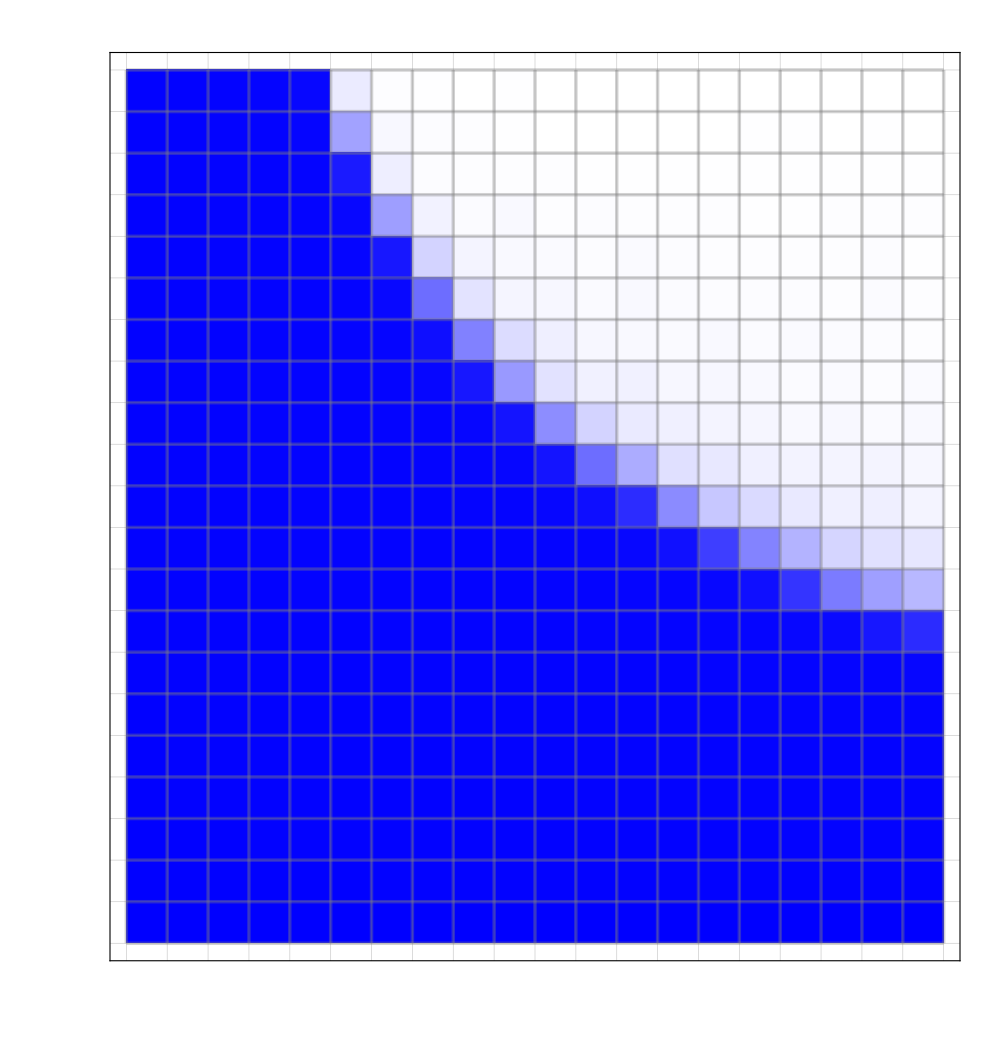

```mathematica
nData=Flatten/@Table[
Cases[filtered,{i,j,c_}->c]
,{i,iOne},{j,iTwo}];
MatrixPlot[Transpose@(Reverse/@nData)
,ColorFunction->(cf1[#]&)
,ColorFunctionScaling->False
,FrameTicks->None(*{{{#,ToString[Rescale[#//N,{25,1},{1,100}]]}&/@Range[1,25,5],None},{Range[0,25,5],None}}*)
,FrameTicksStyle->Directive[65]
,GridLines->{Range[0,20,1],Range[0,100,1]}
,Mesh->All
,MeshStyle->Directive[Gray,Thickness[.0025],Opacity[.35]]
,ImageSize->1000
,PlotRangePadding->0
]
```

### Explore

```mathematica
experiment="UDMelRemediation";
day=timeRange[[2]];
flattenedData={#[[1]],#[[2]],Round[#[[3]]],#[[4]]}&/@ToExpression[Import[experiment<>".csv"]];
x=If[( Length[StringCases[experiment,_~~"R"~~_]]<1),0,1];
filtered=Cases[flattenedData,{a_,b_,day,c_}->{a,b,c}];
{firstCol,firstRow}=ConstantArray[x,2];
probe=Flatten[{
{Round[#[[1]]], #[[2]] ,Clip[#[[3]],{0,1}]}&/@filtered,
Transpose[{
ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],
flattenedData[[All,2]]//DeleteDuplicates,
ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length]
}],
Transpose[{
flattenedData[[All,1]]//DeleteDuplicates,
ConstantArray[firstRow,flattenedData[[All,1]]//DeleteDuplicates//Length],
ConstantArray[firstRow,flattenedData[[All,1]]//DeleteDuplicates//Length]
}]
},1];
```

```mathematica
probe;
matches=Sort[Cases[probe,{6,_,_}]]
```

{{6,0.,1.},{6,0.05,0.99459},{6,0.1,0.99272},{6,0.15,0.99147},{6,0.2,0.99136},{6,0.25,0.99132},{6,0.3,0.99051},{6,0.35,0.99041},{6,0.4,0.98996},{6,0.45,0.98897},{6,0.5,0.98909},{6,0.55,0.98819},{6,0.6,0.98782},{6,0.65,0.98697},{6,0.7,0.98614},{6,0.75,0.9838},{6,0.8,0.98098},{6,0.85,0.97255},{6,0.9,0.89708},{6,0.95,0.36305},{6,1.,0.0785}}

```mathematica
cf1=(Blend[{Directive[{hexToRGB["#ffffff"],Opacity[1]}],Directive[{RGBColor[0, 0, 1],Opacity[.85]}]},#1]&);
cf1[#]&/@matches[[All,3]]
```

{RGBColor[0., 0., 1., 0.85],RGBColor[0.005410000000000026, 0.005410000000000026, 1., 0.8508114999999999],RGBColor[0.007279999999999953, 0.007279999999999953, 1., 0.851092],RGBColor[0.008530000000000038, 0.008530000000000038, 1., 0.8512795],RGBColor[0.008639999999999981, 0.008639999999999981, 1., 0.8512959999999999],RGBColor[0.008680000000000021, 0.008680000000000021, 1., 0.851302],RGBColor[0.009489999999999998, 0.009489999999999998, 1., 0.8514235],RGBColor[0.009589999999999987, 0.009589999999999987, 1., 0.8514385],RGBColor[0.010040000000000049, 0.010040000000000049, 1., 0.851506],RGBColor[0.011029999999999984, 0.011029999999999984, 1., 0.8516545],RGBColor[0.010909999999999975, 0.010909999999999975, 1., 0.8516364999999999],RGBColor[0.011809999999999987, 0.011809999999999987, 1., 0.8517715],RGBColor[0.012179999999999969, 0.012179999999999969, 1., 0.851827],RGBColor[0.013029999999999986, 0.013029999999999986, 1., 0.8519545],RGBColor[0.013859999999999983, 0.013859999999999983, 1., 0.852079],RGBColor[0.016199999999999992, 0.016199999999999992, 1., 0.85243],RGBColor[0.019020000000000037, 0.019020000000000037, 1., 0.852853],RGBColor[0.027449999999999974, 0.027449999999999974, 1., 0.8541175],RGBColor[0.10292000000000001, 0.10292000000000001, 1., 0.8654379999999999],RGBColor[0.63695, 0.63695, 1., 0.9455425],RGBColor[0.9215, 0.9215, 1., 0.988225]}

Response Surface: Sensitivity for Two Nodes

```mathematica
cf2=(Blend[{{-1,Directive[RGBColor[0.0006103608758678569, 0., 1],Opacity[1]]},{0,Directive[RGBColor[1, 1, 0.9850156404974442],Opacity[1]]},{1,Directive[RGBColor[1, 0, 0],Opacity[1]]}},#1]&);
Table[
day=timeRange[[2]];
x=If[( Length[StringCases[experiment,_~~"R"~~_]]<1),0,1];
{firstCol,firstRow}=ConstantArray[x,2];
flattenedData={#[[1]],#[[2]]*100,#[[3]]}&/@ToExpression[Import[experiment<>".csv"]];
contour=ListDensityPlot[
Flatten[{
{#[[1]],#[[2]],Chop[If[#[[3]]>1,1,If[#[[3]]<0,0,#[[3]]]],10^-10]}&/@flattenedData,
Transpose[{
ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],
flattenedData[[All,2]]//DeleteDuplicates,
ConstantArray[0,flattenedData[[All,2]]//DeleteDuplicates//Length]
}]}
,1]
,ColorFunction->cf2
,ColorFunctionScaling->False
,ClippingStyle->White
,GridLines->{Range[-.5,20.5,1],Range[-102.5,100.5,5]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
,FrameTicks->{{{#,ToString[#*1//Round]}&/@Range[0,100,25],None},{Range[0,25,5],None}}
,FrameTicksStyle->Directive[65]
,PlotRange->{{-.5,20.5},{-2.5,102.5},{-1,1}}
,PlotRangePadding->0
];
(*Print[{#//Min,#//Mean,#//Max}&/@{flattenedData[[All,3]]}];*)
Export["./images/"<>experiment<>".png",contour,ImageResolution->500];
Print[experiment];
,{experiment,experimentsList}];
```

Translocations_0001_SA

Translocations_0002_SA

Translocations_0010_SA

Translocations_0020_SA

Translocations_0100_SA

Translocations_0200_SA

Translocations_1000_SA

Translocations_2000_SA

TranslocationsRemediation_0001_SA

TranslocationsRemediation_0002_SA

TranslocationsRemediation_0010_SA

TranslocationsRemediation_0020_SA

TranslocationsRemediation_0100_SA

TranslocationsRemediation_0200_SA

TranslocationsRemediation_1000_SA

TranslocationsRemediation_2000_SA

UDMel_0001_SA

UDMel_0002_SA

UDMel_0010_SA

UDMel_0020_SA

UDMel_0100_SA

UDMel_0200_SA

UDMel_1000_SA

UDMel_2000_SA

UDMelRemediation_0001_SA

UDMelRemediation_0002_SA

UDMelRemediation_0010_SA

UDMelRemediation_0020_SA

UDMelRemediation_0100_SA

UDMelRemediation_0200_SA

UDMelRemediation_1000_SA

UDMelRemediation_2000_SA

Wolbachia_0001_SA

Wolbachia_0002_SA

Wolbachia_0010_SA

Wolbachia_0020_SA

Wolbachia_0100_SA

Wolbachia_0200_SA

Wolbachia_1000_SA

Wolbachia_2000_SA

WolbachiaRemediation_0001_SA

WolbachiaRemediation_0002_SA

WolbachiaRemediation_0010_SA

WolbachiaRemediation_0020_SA

WolbachiaRemediation_0100_SA

WolbachiaRemediation_0200_SA

WolbachiaRemediation_1000_SA

WolbachiaRemediation_2000_SA

Response Surface: Batch Migration

```mathematica
cf3=(Blend[{Directive[{hexToRGB["#ffffff"],Opacity[1]}],Directive[{RGBColor[1, 0, 0.5],Opacity[.85]}]},#1]&);
Table[
day=timeRange[[2]];
flattenedData={#[[1]],#[[2]],Round[#[[3]]],#[[4]]}&/@ToExpression[Import[experiment<>".csv"]];
x=If[( Length[StringCases[experiment,_~~"R"~~_]]<1),0,1];
filtered=Cases[flattenedData,{a_,b_,day,c_}->{a,b*10,c}];
{firstCol,firstRow}=ConstantArray[x,2];
contour=ListContourPlot[
Flatten[{
{#[[1]],#[[2]],If[#[[3]]>1,1,If[#[[3]]<0,0,#[[3]]]]}&/@filtered,
Transpose[{
ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],
flattenedData[[All,2]]//DeleteDuplicates,
ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length]
}],
Transpose[{
flattenedData[[All,1]]//DeleteDuplicates,
ConstantArray[firstRow,flattenedData[[All,1]]//DeleteDuplicates//Length],
ConstantArray[firstRow,flattenedData[[All,1]]//DeleteDuplicates//Length]
}]
},1]
,ColorFunction->cf3
,ColorFunctionScaling->False
,GridLines->{Range[-.5,20.5,1],Range[-1.025,.26,.01]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
,FrameTicks->{{{#,ToString[#*100//Round]}&/@Range[0,1,.05],None},{Range[0,25,5],None}}
,FrameTicksStyle->Directive[65]
,PlotRange->{{-.5,20.5},{-.005,.255},{0,1}}
,PlotRangePadding->0
];
Export["./images/"<>experiment<>".png",contour,ImageResolution->500];
Print[experiment];
,{experiment,experimentsList}];
```

Import::nffil: File Translocations_Batch_SA_SA.csv not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{},Symbol[],{}} cannot be transposed.

Transpose::nmtx: The first two levels of {Symbol[],{},{}} cannot be transposed.

ListContourPlot::arrayerr: {Transpose[{{},Symbol[],{}}],Transpose[{Symbol[],{},{}}]} must be a valid array.

Rasterize::bigraster: Not enough memory available to rasterize Notebook expression.

Translocations_Batch_SA_SA

Import::nffil: File UDMel_Batch_SA_SA.csv not found during Import.

Transpose::nmtx: The first two levels of {{},Symbol[],{}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListContourPlot::arrayerr: {Transpose[{{},Symbol[],{}}],Transpose[{Symbol[],{},{}}]} must be a valid array.

Rasterize::bigraster: Not enough memory available to rasterize Notebook expression.

UDMel_Batch_SA_SA

Import::nffil: File Wolbachia_Batch_SA_SA.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

ListContourPlot::arrayerr: {Transpose[{{},Symbol[],{}}],Transpose[{Symbol[],{},{}}]} must be a valid array.

General::stop: Further output of ListContourPlot::arrayerr will be suppressed during this calculation.

Rasterize::bigraster: Not enough memory available to rasterize Notebook expression.

General::stop: Further output of Rasterize::bigraster will be suppressed during this calculation.

Wolbachia_Batch_SA_SA

Response Surface: Fine Scale

```mathematica
cf1=(Blend[{Directive[{hexToRGB["#ffffff"],Opacity[1]}],Directive[{RGBColor[0, 0, 1],Opacity[.85]}]},#1]&);
Table[
day=timeRange[[2]];
flattenedData={#[[1]],#[[2]],Round[#[[3]]],#[[4]]}&/@ToExpression[Import[experiment<>".csv"]];
x=If[( Length[StringCases[experiment,_~~"R"~~_]]<1),0,1];
filtered=Cases[flattenedData,{a_,b_,day,c_}->{a,b,c}];
{firstCol,firstRow}=ConstantArray[x,2];
contour=ListContourPlot[
Flatten[{
{#[[1]],#[[2]],Clip[#[[3]],{0,1}]}&/@filtered,
Transpose[{
ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],
flattenedData[[All,2]]//DeleteDuplicates,
ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length]
}],
Transpose[{
flattenedData[[All,1]]//DeleteDuplicates,
ConstantArray[firstRow,flattenedData[[All,1]]//DeleteDuplicates//Length],
ConstantArray[firstRow,flattenedData[[All,1]]//DeleteDuplicates//Length]
}]
},1]
,ColorFunction->cf1
,ColorFunctionScaling->False
,GridLines->{Range[-.5,20.5,1],Range[-1.025,1.05,.01]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
,FrameTicks->{{{#,ToString[#*100//Round]}&/@Range[0,1,.1],None},{Range[0,25,5],None}}
,FrameTicksStyle->Directive[65]
,PlotRange->{{-.5,10.5},{-.01,.225},{0,1}}
,PlotRangePadding->0
];
Export["./images/"<>experiment<>".png",contour,ImageResolution->500];
Print[experiment];
,{experiment,experimentsList}]
```

Sensitivity: Batch Migration

```mathematica
Transpose[{
ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],
flattenedData[[All,2]]//DeleteDuplicates,
ConstantArray[0,flattenedData[[All,2]]//DeleteDuplicates//Length]
}]
```

{{0,5.,0},{0,15.,0},{0,8.,0},{0,21.,0},{0,11.,0},{0,18.,0},{0,10.,0},{0,12.,0},{0,7.,0},{0,23.,0},{0,1.,0},{0,25.,0},{0,20.,0},{0,9.,0},{0,6.,0},{0,14.,0},{0,16.,0},{0,4.,0},{0,13.,0},{0,22.,0},{0,19.,0},{0,3.,0},{0,24.,0},{0,17.,0},{0,2.,0}}

```mathematica
cf2=(Blend[{{-1,Directive[RGBColor[0.0006103608758678569, 0., 1],Opacity[1]]},{0,Directive[RGBColor[1, 1, 0.9850156404974442],Opacity[1]]},{1,Directive[RGBColor[1, 0, 0],Opacity[1]]}},#1]&);
Table[
day=timeRange[[2]];
x=If[( Length[StringCases[experiment,_~~"R"~~_]]<1),0,1];
{firstCol,firstRow}=ConstantArray[x,2];
flattenedData={#[[1]],#[[2]]*1000,#[[3]]}&/@ToExpression[Import[experiment<>".csv"]];
contour=ListDensityPlot[
Flatten[{
{#[[1]],#[[2]],Clip[#[[3]],{-1,1}]}&/@flattenedData,
Transpose[{
ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],
flattenedData[[All,2]]//DeleteDuplicates,
ConstantArray[0,flattenedData[[All,2]]//DeleteDuplicates//Length]
}],
Transpose[{
flattenedData[[All,1]]//DeleteDuplicates,
ConstantArray[firstRow,flattenedData[[All,1]]//DeleteDuplicates//Length],
ConstantArray[firstRow,flattenedData[[All,1]]//DeleteDuplicates//Length]
}]
},1]
,ColorFunction->cf2
,ColorFunctionScaling->False
,ClippingStyle->None
,GridLines->{Range[-.5,20.5,1],Range[-.5,25.5,1]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
,FrameTicks->{{Range[0,25,5],None},{Range[0,25,5],None}}
,FrameTicksStyle->Directive[65]
,PlotRange->{{-.5,20.5},{-.5,20.5},{0,1}}
,PlotRangePadding->0
];
(*Print[{#//Min,#//Mean,#//Max}&/@{flattenedData[[All,3]]}];*)
Export["./images/"<>experiment<>".png",contour,ImageResolution->500];
Print[experiment];
,{experiment,experimentsList}];
```

TranslocationsBatch_0001_SA

TranslocationsBatch_0002_SA

TranslocationsBatch_0010_SA

TranslocationsBatch_0020_SA

TranslocationsBatch_0100_SA

TranslocationsBatch_0200_SA

TranslocationsBatch_1000_SA

TranslocationsBatch_2000_SA

UDMelBatch_0001_SA

UDMelBatch_0002_SA

UDMelBatch_0010_SA

UDMelBatch_0020_SA

UDMelBatch_0100_SA

UDMelBatch_0200_SA

UDMelBatch_1000_SA

UDMelBatch_2000_SA

WolbachiaBatch_0001_SA

WolbachiaBatch_0002_SA

WolbachiaBatch_0010_SA

WolbachiaBatch_0020_SA

WolbachiaBatch_0100_SA

WolbachiaBatch_0200_SA

WolbachiaBatch_1000_SA

WolbachiaBatch_2000_SA

Sensitivity: Batch Migration SA

```mathematica
cf2=(Blend[{{-1,Directive[RGBColor[0.0006103608758678569, 0., 1],Opacity[1]]},{0,Directive[RGBColor[1, 1, 0.9850156404974442],Opacity[1]]},{1,Directive[RGBColor[1, 0, 0],Opacity[1]]}},#1]&);
Table[
day=timeRange[[2]];
x=If[( Length[StringCases[experiment,_~~"R"~~_]]<1),0,1];
{firstCol,firstRow}=ConstantArray[x,2];
flattenedData={#[[1]],#[[2]]*1000,#[[3]]}&/@ToExpression[Import[experiment<>".csv"]];
contour=ListDensityPlot[
Flatten[{
{#[[1]],#[[2]],Clip[#[[3]],{-1,1}]}&/@flattenedData,
Transpose[{
ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],
flattenedData[[All,2]]//DeleteDuplicates,
ConstantArray[0,flattenedData[[All,2]]//DeleteDuplicates//Length]
}],
Transpose[{
flattenedData[[All,1]]//DeleteDuplicates,
ConstantArray[firstRow,flattenedData[[All,1]]//DeleteDuplicates//Length],
ConstantArray[firstRow,flattenedData[[All,1]]//DeleteDuplicates//Length]
}]
},1]
,ColorFunction->cf2
,ColorFunctionScaling->False
,ClippingStyle->{RGBColor[0.0006103608758678569, 0., 1],RGBColor[1, 0, 0]}
,GridLines->{Range[-.5,20.5,1],Range[-.5,25.5,1]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
,FrameTicks->{{Range[0,25,5],None},{Range[0,25,5],None}}
,FrameTicksStyle->Directive[65]
,PlotRange->{{-.5,20.5},{-.5,20.5},{-1,1}}
,PlotRangePadding->0
];
(*Print[{#//Min,#//Mean,#//Max}&/@{flattenedData[[All,3]]}];*)
Export["./images/"<>experiment<>".png",contour,ImageResolution->500];
Print[experiment];
,{experiment,experimentsList}];
```

TranslocationsBatch_0001_SA

TranslocationsBatch_0002_SA

TranslocationsBatch_0010_SA

TranslocationsBatch_0020_SA

TranslocationsBatch_0100_SA

TranslocationsBatch_0200_SA

TranslocationsBatch_1000_SA

TranslocationsBatch_2000_SA

UDMelBatch_0001_SA

UDMelBatch_0002_SA

UDMelBatch_0010_SA

UDMelBatch_0020_SA

Sensitivity: Resolution Difference

```mathematica
cf2=(Blend[{{-1,Directive[RGBColor[0.0006103608758678569, 0., 1],Opacity[1]]},{0,Directive[RGBColor[1, 1, 0.9850156404974442],Opacity[1]]},{1,Directive[RGBColor[1, 0, 0],Opacity[1]]}},#1]&);
Table[
day=timeRange[[2]];
x=If[( Length[StringCases[experiment,_~~"R"~~_]]<1),0,1];
{firstCol,firstRow}=ConstantArray[x,2];
flattenedData={#[[1]],#[[2]]*100,#[[3]]}&/@ToExpression[Import[experiment<>".csv"]];
contour=ListDensityPlot[
Flatten[{
{#[[1]],#[[2]],Clip[#[[3]],{-1,1}]}&/@flattenedData,
Transpose[{
ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],
flattenedData[[All,2]]//DeleteDuplicates,
ConstantArray[0,flattenedData[[All,2]]//DeleteDuplicates//Length]
}]}
,1]
,ColorFunction->cf2
,ColorFunctionScaling->False
,ClippingStyle->{RGBColor[0.0006103608758678569, 0., 1],RGBColor[1, 0, 0]}
,GridLines->{Range[-.5,20.5,1],Range[-102.5,100.5,5]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
,FrameTicks->{{{#,ToString[#*1//Round]}&/@Range[0,100,25],None},{Range[0,25,5],None}}
,FrameTicksStyle->Directive[65]
,PlotRange->{{-.5,20.5},{-2.5,102.5},{-1,1}}
,PlotRangePadding->0
];
(*Print[{#//Min,#//Mean,#//Max}&/@{flattenedData[[All,3]]}];*)
Export["./images/"<>experiment<>".png",contour,ImageResolution->500];
Print[experiment];
,{experiment,experimentsList}];
```

Translocations_Batch

$Aborted

Timing: Fixation/Remediation for One Node

```mathematica
expString="UDMelRemediation";
flattenedData=Import[Directory[]<>"/"<>expString<>".csv"];
```

## One

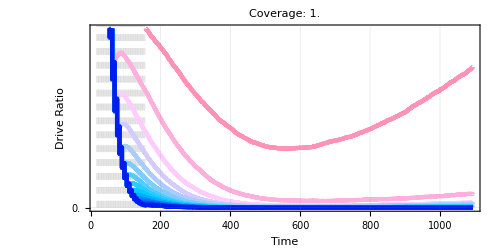

```mathematica
coverage=1.;
If[
(StringTake[expString,{1}]=="T"),
probed=Cases[flattenedData,{#,coverage,_,c_}->c]&/@(flattenedData[[All,1]]//DeleteDuplicates);,
probed=Cases[flattenedData,{#,coverage,_,c_}->1-c]&/@(flattenedData[[All,1]]//DeleteDuplicates);
];
releasesSort=Ordering[flattenedData[[All,1]]//DeleteDuplicates];
plot=ListLinePlot[1-probed[[releasesSort]]
,AspectRatio->.5
,Frame->True
,FrameLabel->(Style[#,50]&/@{"Time","Drive Ratio"})
,FrameStyle->Directive[Thickness[.0025],Gray]
,FrameTicks->{{Range[0,1,.1],None},{Flatten[{Range[0,1000,200]}],None}}
,FrameTicksStyle->20
,GridLines->{Range[0,1000,200],Range[0,1,.25]}
,GridLinesStyle->Directive[Gray,Thick,Opacity[.2]]
,ImageSize->500
,InterpolationOrder->0
,PlotLabel->Style["Coverage: "<>ToString[coverage],40]
,PlotRange->{{20,timeRange[[2]]},{0,.1}}
,PlotStyle->({
Thickness[.006],Blend[{{1,Directive[RGBColor[0.0006103608758678569, 0., 0.9347219043259327],Opacity[1.]]},{.35,Directive[RGBColor[1, 0.8, 1],Opacity[1]]},{.65,Directive[RGBColor[0, 0.8, 1],Opacity[1]]},{0,Directive[RGBColor[1, 0, 0],Opacity[1]]}},#]}&/@Range[0,1,.05])
,Prolog->Flatten[{Opacity[.1],Dashed,Thickness[.004],Line[{{#,0},{#,1}}]&/@(Range[0,7*20-1,1*7]+20)}]
]
```

153

{0.42233,0.44579,0.46956,0.49302,0.51661,0.53766,0.5564,0.31362,0.32279,0.33103,0.33974,0.34872,0.35718,0.36513,0.22565,0.23171,0.23751,0.24319,0.24921,0.25492,0.26047,0.1675,0.17183,0.17578,0.17991,0.18415,0.18828,0.19219,0.12608,0.12918,0.13204,0.13481,0.13766,0.14061,0.1434,0.09493,0.09726,0.09939,0.10156,0.10381,0.10588,0.1079,0.0717,0.07334,0.07494,0.07644,0.07807,0.07963,0.08112,0.0541,0.05525,0.05637,0.05747,0.05859,0.05968,0.06072,0.04052,0.04138,0.04218,0.04294,0.04374,0.04453,0.04531,0.03029,0.0309,0.0315,0.03207,0.03262,0.03315,0.03362,0.02243,0.02288,0.0233,0.02371,0.02414,0.02456,0.02492,0.01659,0.01691,0.01718,0.01745,0.01777,0.01803,0.01829,0.01221,0.01241,0.01262,0.01287,0.01306,0.01325,0.01343,0.0136,0.01363,0.01363,0.01362,0.01363,0.01361,0.01361,0.01363,0.01359,0.01357,0.01357,0.01353,0.01348,0.01339,0.0133,0.01325,0.01316,0.013,0.01293,0.01282,0.01273,0.01261,0.01246,0.01233,0.01218,0.01205,0.01193,0.01179,0.01169,0.01154,0.01148,0.01141,0.01123,0.01109,0.01097,0.01083,0.01072,0.01063,0.01055,0.01047,0.01031,0.01015,0.00999,0.00984,0.00976,0.00963,0.00951,0.00937,0.00933,0.00921,0.00912,0.00903,0.00891,0.00883,0.00873,0.0086,0.00848,0.00837,0.0082,0.00809,0.00795,0.00786,0.00777,0.00768,0.00763,0.00753,0.00742,0.00731,0.0072,0.00711,0.00702,0.00698,0.00687,0.00679,0.00671,0.0066,0.00655,0.00646,0.00637,0.00628,0.00619,0.0061,0.00601,0.00593,0.00583,0.00576,0.00567,0.0056,0.00555,0.0055,0.00543,0.00532,0.00525,0.00521,0.00513,0.00505,0.00495,0.00488,0.00481,0.00474,0.00472,0.00464,0.00461,0.00456,0.00453,0.00447,0.00441,0.00436,0.00429,0.00422,0.00412,0.00405,0.00397,0.00392,0.00385,0.00384,0.0038,0.00372,0.00364,0.00361,0.00357,0.00353,0.00349,0.00345,0.00341,0.00335,0.00326,0.00321,0.00316,0.00311,0.00306,0.003,0.00296,0.00292,0.00288,0.00283,0.00279,0.00274,0.00269,0.00263,0.0026,0.00254,0.00252,0.00252,0.00245,0.0024,0.00236,0.00232,0.00227,0.0022,0.00218,0.00215,0.00213,0.00212,0.0021,0.00208,0.00205,0.00202,0.002,0.00195,0.00192,0.00188,0.00187,0.00183,0.0018,0.00179,0.00176,0.00174,0.00173,0.0017,0.00167,0.00164,0.00162,0.0016,0.00158,0.00154,0.00153,0.0015,0.00148,0.00145,0.00143,0.00141,0.00136,0.00135,0.00133,0.00132,0.00131,0.00129,0.00127,0.00127,0.00126,0.00125,0.00123,0.00121,0.00118,0.00116,0.00114,0.00111,0.00111,0.0011,0.0011,0.00108,0.00106,0.00105,0.00103,0.00102,0.00101,0.00098,0.00096,0.00093,0.00093,0.00093,0.00091,0.0009,0.00089,0.00089,0.00087,0.00085,0.00083,0.00081,0.00082,0.00081,0.0008,0.00079,0.00078,0.00077,0.00076,0.00075,0.00074,0.00072,0.00072,0.0007,0.0007,0.00069,0.00068,0.00067,0.00065,0.00065,0.00064,0.00064,0.00063,0.00063,0.00062,0.0006,0.00058,0.00056,0.00056,0.00055,0.00054,0.00054,0.00054,0.00051,0.00051,0.0005,0.00048,0.00049,0.00049,0.00048,0.00048,0.00048,0.00047,0.00048,0.00048,0.00047,0.00046,0.00046,0.00045,0.00044,0.00043,0.00042,0.00042,0.00043,0.00042,0.00042,0.00041,0.0004,0.0004,0.00039,0.00038,0.00039,0.00037,0.00037,0.00037,0.00035,0.00035,0.00034,0.00034,0.00033,0.00033,0.00033,0.00033,0.00032,0.00032,0.00032,0.00032,0.00034,0.00032,0.00033,0.00033,0.00032,0.00033,0.00032,0.00031,0.0003,0.0003,0.0003,0.00028,0.00027,0.00027,0.00027,0.00027,0.00027,0.00027,0.00027,0.00026,0.00026,0.00026,0.00025,0.00026,0.00026,0.00026,0.00025,0.00025,0.00025,0.00025,0.00024,0.00024,0.00025,0.00025,0.00024,0.00025,0.00025,0.00025,0.00024,0.00024,0.00024,0.00024,0.00024,0.00023,0.00024,0.00024,0.00023,0.00023,0.00023,0.00023,0.00022,0.00022,0.00021,0.00021,0.0002,0.0002,0.0002,0.0002,0.00019,0.0002,0.00021,0.0002,0.00021,0.00021,0.00021,0.00021,0.0002,0.0002,0.0002,0.0002,0.00021,0.00021,0.0002,0.0002,0.0002,0.00021,0.00021,0.00021,0.00021,0.00021,0.00022,0.00022,0.00022,0.00022,0.00021,0.00021,0.00021,0.00021,0.00021,0.00021,0.00022,0.00022,0.00021,0.00022,0.00022,0.0002,0.0002,0.00021,0.0002,0.00021,0.0002,0.0002,0.0002,0.00021,0.00021,0.00021,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.00021,0.00021,0.00021,0.00021,0.00021,0.0002,0.00021,0.00021,0.00021,0.0002,0.00021,0.00021,0.00021,0.00022,0.00022,0.00022,0.00022,0.00022,0.0002,0.0002,0.0002,0.0002,0.00021,0.00022,0.00021,0.00021,0.00022,0.00022,0.00022,0.00021,0.00021,0.00022,0.00023,0.00024,0.00025,0.00024,0.00025,0.00024,0.00024,0.00025,0.00025,0.00025,0.00025,0.00025,0.00025,0.00025,0.00025,0.00025,0.00025,0.00025,0.00024,0.00024,0.00023,0.00022,0.00023,0.00023,0.00022,0.00023,0.00023,0.00023,0.00023,0.00022,0.00022,0.00023,0.00023,0.00023,0.00023,0.00022,0.00022,0.00024,0.00023,0.00024,0.00024,0.00024,0.00023,0.00023,0.00023,0.00024,0.00024,0.00024,0.00024,0.00024,0.00023,0.00023,0.00023,0.00024,0.00023,0.00024,0.00024,0.00024,0.00025,0.00025,0.00024,0.00023,0.00023,0.00024,0.00022,0.00022,0.00023,0.00024,0.00024,0.00024,0.00025,0.00024,0.00024,0.00025,0.00025,0.00025,0.00024,0.00024,0.00023,0.00023,0.00022,0.00022,0.00023,0.00023,0.00024,0.00024,0.00024,0.00025,0.00025,0.00025,0.00025,0.00026,0.00025,0.00025,0.00027,0.00028,0.00027,0.00028,0.00027,0.00026,0.00027,0.00027,0.00027,0.00027,0.00027,0.00028,0.00028,0.00028,0.00028,0.00027,0.00028,0.00028,0.00027,0.00028,0.00029,0.00029,0.0003,0.0003,0.00029,0.0003,0.00029,0.00029,0.0003,0.00032,0.00032,0.00032,0.00031,0.00031,0.0003,0.00031,0.0003,0.00029,0.00028,0.00028,0.00028,0.00028,0.00027,0.00027,0.00027,0.00028,0.00028,0.00028,0.00029,0.00028,0.00027,0.00027,0.00026,0.00028,0.00029,0.00029,0.00029,0.0003,0.00029,0.00029,0.00029,0.00029,0.0003,0.0003,0.00029,0.0003,0.00031,0.00033,0.00032,0.00032,0.00032,0.00031,0.00031,0.00031,0.00029,0.00029,0.00029,0.0003,0.00031,0.00031,0.00031,0.0003,0.0003,0.0003,0.0003,0.0003,0.0003,0.0003,0.0003,0.00031,0.00029,0.00029,0.00028,0.00029,0.00029,0.0003,0.0003,0.00031,0.00031,0.00031,0.0003,0.00029,0.00029,0.00028,0.00028,0.00028,0.00029,0.00028,0.00029,0.00029,0.00029,0.0003,0.0003,0.00031,0.0003,0.00031,0.00029,0.00031,0.00031,0.00031,0.0003,0.00031,0.00032,0.00032,0.00032,0.00032,0.00033,0.00033,0.00035,0.00035,0.00035,0.00034,0.00034,0.00035,0.00035,0.00035,0.00034,0.00035,0.00035,0.00035,0.00035,0.00035,0.00035,0.00035,0.00034,0.00033,0.00033,0.00034,0.00035,0.00035,0.00035,0.00036,0.00036,0.00035,0.00035,0.00035,0.00036,0.00037,0.00037,0.00038,0.00039,0.00038,0.00038,0.00039,0.00038,0.00037,0.00037,0.00037,0.00037,0.00039,0.00039,0.00039,0.00039,0.00039,0.0004,0.00038,0.00037,0.00038,0.00038,0.00038,0.00038,0.00038,0.00039,0.00039,0.00039,0.0004,0.0004,0.0004,0.00041,0.0004,0.0004,0.0004,0.0004,0.00041,0.0004,0.00041,0.0004,0.00037,0.00038,0.00039,0.00038,0.00038,0.00038,0.00038,0.00039,0.00038,0.00038,0.00038,0.00039,0.0004,0.00042,0.00043,0.00043,0.00044,0.00044,0.00044,0.00045,0.00045,0.00045,0.00045,0.00044,0.00045,0.00044,0.00043,0.00043,0.00046,0.00048,0.0005,0.00049,0.00049,0.00049,0.00049,0.00049,0.00048,0.00048,0.00049,0.00049,0.00049,0.00051,0.00048,0.00049,0.00049,0.0005,0.00048,0.00047,0.00048,0.00049,0.00048,0.00049,0.00048,0.0005,0.0005,0.00049,0.00051,0.0005,0.00053,0.00052,0.00053,0.00052,0.00053,0.00054,0.00053,0.00052,0.00054,0.00055,0.00055,0.00056,0.00055,0.00055,0.00055,0.00057,0.00057,0.00058,0.00058,0.00059,0.00059,0.00059,0.00059,0.0006,0.00061,0.0006,0.00058,0.00059,0.00058,0.00058,0.00058,0.00058,0.00057,0.00059,0.00059,0.0006,0.0006,0.00061,0.0006,0.00059,0.00059,0.00058,0.00058,0.00058,0.00058,0.00058,0.00059,0.00061,0.00062,0.00061,0.00061,0.00061,0.0006,0.0006,0.0006,0.0006,0.0006,0.00061,0.00062,0.00061,0.0006,0.0006,0.00059,0.00058,0.00058,0.00058,0.00058,0.00061,0.00062,0.00062,0.00062,0.0006,0.00061,0.00061,0.0006,0.00061,0.0006,0.00062,0.00061,0.00062,0.00061,0.00062,0.00064,0.00062,0.00063,0.00063,0.00062,0.00062,0.00065,0.00067,0.00067,0.00067,0.00066,0.00067,0.00068,0.00069,0.00071,0.00069,0.0007,0.00071,0.00072,0.00075,0.00075,0.00075,0.00076,0.00075,0.00075,0.00074,0.00073,0.00073,0.00072,0.00074,0.00077,0.00077,0.00081,0.0008,0.00082,0.00082,0.00081,0.0008,0.00081,0.00083,0.00081,0.00081,0.00083,0.00082,0.00083,0.00083,0.00085,0.00086,0.00087,0.00086,0.00087,0.00087,0.00086,0.00084,0.00084,0.00087,0.00086,0.00086,0.00089,0.00091,0.00093,0.00092,0.00092,0.00093,0.00093,0.00095,0.00095,0.00093,0.00091,0.00091,0.00091,0.00092,0.00091,0.00094,0.00096,0.00093,0.00091,0.00091,0.00093,0.00093,0.00093,0.00093,0.00094,0.00095,0.00096,0.00094,0.00093,0.0009,0.00092,0.00092,0.00091,0.00092,0.00093,0.00096,0.00096,0.00097,0.00097,0.00096,0.00094,0.00094,0.00094,0.00092,0.00093,0.00094,0.00098,0.00097,0.00096,0.00098,0.00096,0.00097,0.00099,0.00099,0.00099,0.00099}

3

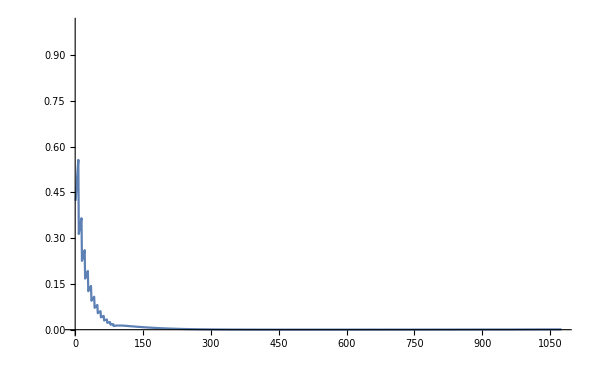

```mathematica
sample=13;
lastRelease=(Range[0,7*20-1,1*7]+20)//Last
probe=1-probed[[releasesSort]][[sample]][[20;;All]]
Count[(#<(1-.5)&)/@probe, False]
ListLinePlot[probe,PlotRange->{0,1}]
```

```mathematica
lastRelease=(Range[0,7*20-1,1*7]+20)//Last
probed[[10]]//Last
```

153

0.00007

```mathematica
range=Range[1,20,1];
blends=Blend[{{1,Directive[RGBColor[0.0006103608758678569, 0., 0.9347219043259327],Opacity[1.]]},{.35,Directive[RGBColor[1, 0.8, 1],Opacity[1]]},{.65,Directive[RGBColor[0, 0.8, 1],Opacity[1]]},{0,Directive[RGBColor[1, 0, 0],Opacity[1]]}},#]&/@Range[.05,1,.05];
colorScale=Transpose[{
Reverse[ImageResize[Rasterize[#]//ImageCrop,50]&/@blends],
Reverse[Style[ToString[#],35]&/@range]
}]//Grid;
Export["./images/CoverageSweeps/colorScale.pdf",colorScale]
```

## Batch

```mathematica
Table[
expStringSample=j;
x=If[( Length[StringCases[expStringSample,_~~"R"~~_]]<1),0,1];
dID=(StringTake[expStringSample,{1}]=="T");
flattenedData=Import[Directory[]<>"/"<>expStringSample<>".csv"];
Table[
coverage=i;
If[dID,
probed=Cases[flattenedData,{#,coverage,_,c_}->Abs[x-(x-c)/1]]&/@(flattenedData[[All,1]]//DeleteDuplicates);,
probed=Cases[flattenedData,{#,coverage,_,c_}->Abs[x-(x-(1-c))/1]]&/@(flattenedData[[All,1]]//DeleteDuplicates);
];
releasesSort=Ordering[flattenedData[[All,1]]//DeleteDuplicates];
plot=ListLinePlot[probed[[releasesSort]]
,AspectRatio->1
,Frame->True
(*,FrameLabel->(Style[#,60]&/@{"Time","Drive Ratio"})*)
,FrameStyle->Directive[Thickness[.0075],Gray,50]
,FrameTicks->None
,FrameTicksStyle->20
,GridLines->{Range[0,1000,200],Range[0,1,.25]}
,GridLinesStyle->Directive[Gray,Thick,Opacity[.2]]
,ImageSize->500
,InterpolationOrder->1
,PlotRange->{{20,500},{0,1}}
,PlotStyle->({
Thickness[.007],Blend[{{1,Directive[RGBColor[0.0006103608758678569, 0., 0.9347219043259327],Opacity[1.]]},{.35,Directive[RGBColor[1, 0.8, 1],Opacity[1]]},{.65,Directive[RGBColor[0, 0.8, 1],Opacity[1]]},{0,Directive[RGBColor[1, 0, 0],Opacity[1]]}},#]}&/@Range[0,1,.05])
,Prolog->Flatten[{Opacity[.25],Thickness[.001],Line[{{#,0},{#,1}}]&/@(Range[0,7*20-1,1*7]+20)}]
];
Export["./images/CoverageSweeps/"<>expStringSample<>StringPadLeft[ToString[coverage*100],4,"0"]<>"png",plot,ImageSize->1000]
,{i,flattenedData[[All,2]]//DeleteDuplicates}];
,{j,experimentsList}]
```

Legends

```mathematica
BarLegend[{(Blend[{{0,Directive[RGBColor[1, 1, 1],Opacity[1]]},{1,Directive[RGBColor[1, 0, 0.5],Opacity[1]]}},#]&),{0,1}}]
Export["./images/colorScaleBatch.pdf",%,ImageSize->500]
BarLegend[{(Blend[{Directive[{hexToRGB["#ffffff"],Opacity[1]}],Directive[{RGBColor[0, 0, 1],Opacity[.85]}]},#1]&),{0,1}}]
Export["./images/colorScale.pdf",%,ImageSize->500]
BarLegend[{(Blend[{{0,Directive[RGBColor[1, 1, 1],Opacity[1]]},{1,Directive[RGBColor[0, 0, 0.5],Opacity[1]]}},#]&),{0,1}}]
Export["./images/colorScaleSensitivity.pdf",%,ImageSize->500]
BarLegend[{Blend[{{-1,Directive[RGBColor[0.0006103608758678569, 0., 1],Opacity[1]]},{0,Directive[RGBColor[1, 1, 0.9850156404974442],Opacity[1]]},{1,Directive[RGBColor[1, 0, 0],Opacity[1]]}},#1]&,{-1,1}}]
Export["./images/colorScaleSensitivity2.pdf",%,ImageSize->500]
```

```mathematica
SwatchLegend[
{ColorData[{"DeepSeaColors",{0,1}}][0],ColorData[{"DeepSeaColors",{0,1}}][1]},
{"0% Drive","100% Drive"}
,LegendMarkerSize->50
,LabelStyle->50
]
Export["swatchFixation.pdf",%]
```

## Old

Response Surface: Fixation/Remediation for One Node

```mathematica
cf1=(Blend[{Directive[{hexToRGB["#ffffff"],Opacity[1]}],Directive[{RGBColor[0, 0, 1],Opacity[.85]}]},#1]&);
Table[
day=timeRange[[2]];
flattenedData={#[[1]],#[[2]],Round[#[[3]]],#[[4]]}&/@ToExpression[Import[experiment<>".csv"]];
x=If[( Length[StringCases[experiment,_~~"R"~~_]]<1),0,1];
filtered=Cases[flattenedData,{a_,b_,day,c_}->{a,b,c}];
{firstCol,firstRow}=ConstantArray[x,2];
contour=ListContourPlot[
Flatten[{
{#[[1]],#[[2]],If[#[[3]]>1,1,If[#[[3]]<0,0,#[[3]]]]}&/@filtered,
Transpose[{
ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],
flattenedData[[All,2]]//DeleteDuplicates,
ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length]
}],
Transpose[{
flattenedData[[All,1]]//DeleteDuplicates,
ConstantArray[firstRow,flattenedData[[All,1]]//DeleteDuplicates//Length],
ConstantArray[firstRow,flattenedData[[All,1]]//DeleteDuplicates//Length]
}]
},1]
,ColorFunction->cf1
,ColorFunctionScaling->False
,GridLines->{Range[-.5,20.5,1],Range[-1.025,1.05,.05]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
,FrameTicks->{{{#,ToString[#*100//Round]}&/@Range[0,1,.25],None},{Range[0,25,5],None}}
,FrameTicksStyle->Directive[65]
,PlotRange->{{-.5,20.5},{-.025,1.025},{0,1}}
,PlotRangePadding->0
];
Export["./images/"<>experiment<>".png",contour,ImageResolution->500];
Print[experiment];
,{experiment,experimentsList}]
```

Response Surface (Sensitivity)

## Single Experiment

```mathematica
day=999;
experimentString="UXSA_200";
flattenedData={#[[1]],#[[2]],Round[#[[3]]],#[[4]]}&/@ToExpression[Import["./"<>experimentString<>".csv"]];
filtered=Cases[flattenedData,{a_,b_,day,c_}->{a,b,1-c}];
{firstCol,firstRow}=ConstantArray[0,2];
contour=ListDensityPlot[
Flatten[{
filtered,
Transpose[{ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],
flattenedData[[All,2]]//DeleteDuplicates,ConstantArray[firstRow,flattenedData[[All,2]]//DeleteDuplicates//Length]}]},1]
,ColorFunction->(Blend[{{0,Directive[RGBColor[1, 1, 1],Opacity[1]]},{1,Directive[RGBColor[0, 0, 0.5],Opacity[1]]}},#]&)
,ColorFunctionScaling->False
,GridLines->{Range[-.5,20.5,1],Range[-1.025,1.05,.05]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
(*,FrameLabel->(Style[#,75]&/@{"Releases Number","Coverage"})*)
,FrameTicks->{{{#,ToString[#*100//Round]}&/@Range[0,1,.25],None},{Range[0,25,5],None}}
,FrameTicksStyle->Directive[65]
,PlotRange->{{-.5,20.5},{-.025,1.025}}
,PlotRangePadding->0
]
Export["./images/"<>experimentString<>".pdf",contour,ImageSize->1000]
```

## Batch Experiment

```mathematica
expIDS={"T","U"};
expIDN=Flatten[{("XSA_"<>#),("RSA_"<>#)}&/@{"001","002","010","020","100","200"}];
expStrings=Table[(i<>#)&/@expIDN,{i,expIDS}]
```

```mathematica
Table[
Table[
experimentString=expStrings[[i,j]];
(**)
flattenedData={#[[1]],#[[2]],Round[#[[3]]],#[[4]]}&/@ToExpression[Import["./"<>experimentString<>".csv"]];
filtered=Cases[flattenedData,{a_,b_,day,c_}->{a,b,c}];
filtered=If[i==1,filtered,{#[[1]],#[[2]],1-#[[3]]}&/@filtered];
{firstCol,firstRow}=If[(i==1)&&(StringTake[experimentString,{2}]=="R"),ConstantArray[0,2],ConstantArray[1,2]];
{firstCol,firstRow}=If[(i==2)&&(StringTake[experimentString,{2}]=="X"),ConstantArray[0,2],ConstantArray[1,2]];
(**)
contour=ListDensityPlot[
Flatten[{
filtered,
Transpose[{ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],
flattenedData[[All,2]]//DeleteDuplicates,ConstantArray[firstRow,flattenedData[[All,2]]//DeleteDuplicates//Length]}]},1]
,ColorFunction->(Blend[{{0,Directive[RGBColor[1, 1, 1],Opacity[1]]},{1,Directive[RGBColor[0, 0, 0.5],Opacity[1]]}},#]&)
,ColorFunctionScaling->False
,GridLines->{Range[-.5,20.5,1],Range[-1.025,1.05,.05]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
(*,FrameLabel->(Style[#,75]&/@{"Releases Number","Coverage"})*)
,FrameTicks->{{{#,ToString[#*100//Round]}&/@Range[0,1,.25],None},{Range[0,25,5],None}}
,FrameTicksStyle->Directive[65]
,PlotRange->{{-.5,20.5},{-.025,1.025}}
,PlotRangePadding->0
];
Export["./imagesFinal/SA_N_"<>experimentString<>".pdf",contour,ImageSize->1000]
,{j,1,Length[expStrings[[i]]]}]
,{i,1,2}]
```

Response Surface (Sensitivity Difference)

## Single Experiment

```mathematica
experimentString="UXSA_0002Diff";
{firstCol,firstRow}=ConstantArray[0,2];
flattenedData=Chop[Import["./"<>experimentString<>".csv"],10^-2];
{flattenedData[[All,3]]//Max,flattenedData//Min}
flattenedData[[All,3]]//Sort;
dominant=If[Total[flattenedData[[All,3]]]<0,-1,1];
flattenedData={#[[1]],#[[2]]*10,If[#[[3]]<0,#[[3]],dominant*(#[[3]])]}&/@flattenedData;
```

```mathematica
contour=ListDensityPlot[Flatten[{flattenedData,Transpose[{ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],flattenedData[[All,2]]//DeleteDuplicates,ConstantArray[0,flattenedData[[All,2]]//DeleteDuplicates//Length]}]},1]
,ColorFunction->(Blend[{{-1,Directive[RGBColor[0.0006103608758678569, 0., 1],Opacity[1]]},{0,Directive[RGBColor[1, 1, 0.9850156404974442],Opacity[1]]},{1,Directive[RGBColor[1, 0, 0],Opacity[1]]}},#]&)
,ColorFunctionScaling->False
,ClippingStyle->Black
,GridLines->{Range[-.5,20.5,1],Range[-102.5,100.5,5]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
(*,FrameLabel->(Style[#,75]&/@{"Releases Number","Coverage"})*)
,FrameTicks->{{{#,ToString[#*1//Round]}&/@Range[0,100,25],None},{Range[0,25,5],None}}
,FrameTicksStyle->Directive[65]
,PlotRange->{{-.5,20.5},{-2.5,102.5},{-1,1}}
,PlotRangePadding->0
]
Export["./images/"<>experimentString<>".pdf",contour,ImageSize->1000]
```

## Batch Experiment

```mathematica
expIDS={"T","U"};
expIDN=Flatten[{("XSA_"<>#<>"Diff"),("RSA_"<>#<>"Diff")}&/@{"001","002","010","020","100","200"}];
expStrings=Table[(i<>#)&/@expIDN,{i,expIDS}]
```

```mathematica
Table[
Table[
experimentString=expStrings[[i,j]];
{firstCol,firstRow}=ConstantArray[0,2];
flattenedData=Chop[Import["./"<>experimentString<>".csv"],10^-2];
dominant=If[Total[flattenedData[[All,3]]]<0,-1,1];
flattenedData={#[[1]],#[[2]],If[#[[3]]<0,#[[3]],1*(#[[3]])]}&/@flattenedData;
flattenedData=If[i==1,flattenedData,{#[[1]],#[[2]],-1*#[[3]]}&/@flattenedData];
(**)
contour=ListDensityPlot[Flatten[{flattenedData,Transpose[{ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],flattenedData[[All,2]]//DeleteDuplicates,ConstantArray[0,flattenedData[[All,2]]//DeleteDuplicates//Length]}]},1]
,ColorFunction->(Blend[{{-1,Directive[RGBColor[0.0006103608758678569, 0., 1],Opacity[1]]},{0,Directive[RGBColor[1, 1, 0.9850156404974442],Opacity[1]]},{1,Directive[RGBColor[1, 0, 0],Opacity[1]]}},#]&)
,ColorFunctionScaling->False
,ClippingStyle->Black
,GridLines->{Range[-.5,20.5,1],Range[-1.025,1.05,.05]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
(*,FrameLabel->(Style[#,75]&/@{"Releases Number","Coverage"})*)
,FrameTicks->{{{#,ToString[#*100//Round]}&/@Range[0,1,.25],None},{Range[0,25,5],None}}
,FrameTicksStyle->Directive[65]
,PlotRange->{{-.5,20.5},{-.025,1.025},{-1,1}}
,PlotRangePadding->0
];
Export["./imagesFinal/SA_D_"<>experimentString<>".pdf",contour,ImageSize->1000]
,{j,1,Length[expStrings[[i]]]}]
,{i,1,2}]
```

Response Surface (Batch Migration Sensitivity)

```mathematica
day=1093;
experimentString="UBSA_200Diff";
multiplier=1;
flattenedData=Chop[Import["./"<>experimentString<>".csv"],10^-2];
(*{flattenedData[[All,3]]//Max,flattenedData//Min}
flattenedData[[All,3]]//Sort;
dominant=If[Total[flattenedData[[All,3]]]<0,-1,1];
flattenedData={#[[1]],#[[2]]*multiplier,2*If[#[[3]]<0,#[[3]],dominant*(#[[3]])]}&/@flattenedData;*)
ListDensityPlot[flattenedData,InterpolationOrder->0];
flattenedData[[All,3]]//Sort;
```

```mathematica
contour=ListDensityPlot[Flatten[{flattenedData,Transpose[{flattenedData[[All,1]]//DeleteDuplicates,ConstantArray[0,flattenedData[[All,1]]//DeleteDuplicates//Length],ConstantArray[0,flattenedData[[All,1]]//DeleteDuplicates//Length]}]},1]
,ColorFunction->(Blend[{{-1,Directive[RGBColor[0.0006103608758678569, 0., 1],Opacity[1]]},{0,Directive[RGBColor[1, 1, 0.9850156404974442],Opacity[1]]},{1,Directive[RGBColor[1, 0, 0],Opacity[1]]}},#]&)
,ColorFunctionScaling->False
,GridLines->{Range[-.5,41,1],Range[-.005,.25,.01]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
(*,FrameLabel->(Style[#,75]&/@{"Releases Number","Coverage"})*)
,FrameTicks->{{{#,ToString[#*100//Round]}&/@Range[0,.25,.05],None},{Range[0,40,10],None}}
,FrameTicksStyle->Directive[Bold,65]
,PlotLegends->None
,PlotRange->{{-.5,20.5},{-.005,.255},{-1,1}}
,PlotRangePadding->0
]
Export["./images/"<>experimentString<>".pdf",contour,ImageSize->1000]
```

Explore

```mathematica
cf1=(Blend[{Directive[{hexToRGB["#ffffff"],Opacity[1]}],Directive[{RGBColor[0, 0, 1],Opacity[.85]}]},#1]&);
experiment="UDMelRemediation";
day=timeRange[[2]];
flattenedData={#[[1]],#[[2]],Round[#[[3]]],#[[4]]}&/@ToExpression[Import[experiment<>".csv"]];
x=If[(StringTake[experiment,{2}]=="X"),0,1];
filtered=Cases[flattenedData,{a_,b_,day,c_}->{a,b,c}];
{firstCol,firstRow}=ConstantArray[x,2];
contour=ListContourPlot[
Flatten[{
filtered,
Transpose[{
ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],
flattenedData[[All,2]]//DeleteDuplicates,
ConstantArray[firstRow,flattenedData[[All,2]]//DeleteDuplicates//Length]
}]},1]
,ColorFunction->cf1
,ColorFunctionScaling->False
,GridLines->{Range[-.5,20.5,1],Range[-1.025,1.05,.05]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
,FrameTicks->{{{#,ToString[#*100//Round]}&/@Range[0,1,.25],None},{Range[0,25,5],None}}
,FrameTicksStyle->Directive[65]
,PlotRange->{{-.5,20.5},{-.025,1.025},{filtered[[All,3]]//Min,filtered[[All,3]]//Max}}
,PlotRangePadding->0
]
```

Timing

```mathematica
experimentString=experimentString="E_02_05_0001_0050";
flattenedData=Import["./"<>experimentString<>".csv"][[2;;All]];
```

```mathematica
i=1;
releasesNumber=flattenedData[[All,1]]//DeleteDuplicates
probed=Cases[flattenedData,{#,coverage,_,c_}->1-c]&/@releasesNumber
```

```mathematica
Table[
coverage=i;
releasesNumber=flattenedData[[All,1]]//DeleteDuplicates;
probed=Cases[flattenedData,{#,coverage,_,c_}->1-c]&/@releasesNumber;
plot=ListLinePlot[probed
,AspectRatio->1
,Filling->Prepend[(#->{#+1})&/@Range[1,Length[probed]-1],1->1]
,FillingStyle->Opacity[0]
,Frame->True
,FrameStyle->Directive[Thickness[.0075],Gray,50]
,FrameTicks->None(*{{{#,StringPadRight[ToString[#],4,"0"]}&/@Range[0,1,.5],None},{Flatten[{Range[0,1000,200]}],None}}*)
,FrameTicksStyle->30
,GridLines->{Range[0,1000,200],Range[0,1,.25]}
,GridLinesStyle->Directive[Gray,Thick,Opacity[.2]]
,ImageSize->1000
,InterpolationOrder->0
,PlotRange->{{9*20,1000},{0,1}}
,PlotStyle->({Thickness[.005],Blend[{{0,Directive[RGBColor[1, 0.5, 1],Opacity[1]]},{1,Directive[RGBColor[0, 0, 1],Opacity[1]]}},#]}&/@Range[0,1,.05])
,Prolog->Flatten[{Opacity[.2],Dashed,Thickness[.001],Line[{{#,0},{#,1}}]&/@(Range[0,7*20-1,1*7]+20)}]
];
Export["./"<>experimentString<>"_"<>StringPadLeft[ToString[coverage*100//Round],4,"0"]<>".png",plot,ImageSize->1000]
,{i,flattenedData[[All,2]]//DeleteDuplicates}]
```

```mathematica
Line[{ConstantArray[0,probed[[2]]//Length],Range[1,probed[[2]]//Length],probed[[2]]}//Transpose]
```

```mathematica
Range[First[releasesNumber],Last[releasesNumber],4]
releasesNumber
```

```mathematica
two=Blend[{{0,Directive[RGBColor[1, 0.5, 1],Opacity[1]]},{1,Directive[RGBColor[0, 0, 1],Opacity[1]]}},#]&/@Range[0,1,1]
SwatchLegend[two,{"1 release","20 releases"}]
```

```mathematica
BarLegend[{Blend[{{0,Directive[RGBColor[1, 0.5, 1],Opacity[1]]},{1,Directive[RGBColor[0, 0, 1],Opacity[1]]}},#]&,{0,1}},20]
Export["swatch.pdf",%,ImageSize->1000]
```

```mathematica
(#->{#+1})&/@Range[2,10]
```